# ROC for classifier ensembles, bootstrapping, damaging, and interpolation

## Introduction

The main goals of this document are:

i) to demonstrate how to create versions and combinations of classifiers utilizing different perspectives,

ii) to apply the Receiver Operating Characteristic (ROC) technique into evaluating the created classifiers (see [2,3]) and

iii) to illustrate the use of the Mathematica packages [5,6].

The concrete steps taken are the following:

1. Obtain data: Mathematica built-in or external. Do some rudimentary analysis.

2. Create an ensemble of classifiers and compare its performance to the individual classifiers in the ensemble.

3. Produce classifier versions with from changed data in order to explore the effect of records outliers.

4. Make a bootstrapping classifier ensemble and evaluate and compare its performance.

5. Systematically diminish the training data and evaluate the results with ROC.

6. Show how to do classifier interpolation utilizing ROC.

In the steps above we skip the necessary preliminary data analysis. For the datasets we use in this document that analysis has been done elsewhere. (See [,,,].) Nevertheless, since ROC is mostly used for binary classifiers we want to analyze the class labels distributions in the datasets in order to designate which class labels are “positive” and which are “negative.”

### ROC plots evaluation (in brief)

Assume we are given a binary classifier with the class labels P and N (for “positive” and “negative” respectively).

Consider the following measures True Positive Rate (TPR):

TPR:=(correctly classified positives)/(total positives).

and False Positive Rate (FPR):

FPR:=(incorrectly classified negatives)/(total negatives).

Assume that we can change the classifier results with a parameter θ and produce a plot like this one:

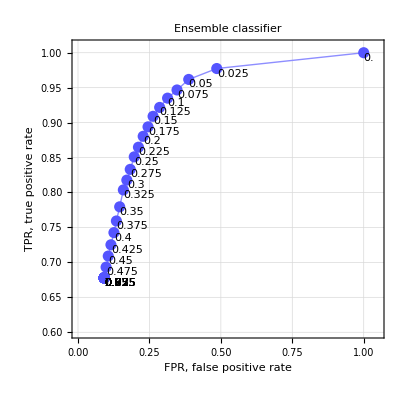

For each parameter value θ_i the point {TPR(θ_i),FPR(θ_i)} is plotted; points corresponding to consecutive θ_i’s are connected with a line. We call the obtained curve the ROC curve for the classifier in consideration. The ROC curve resides in the ROC space as defined by the functions FPR and TPR corresponding respectively to the x-axis and the y-axis.

The ideal classifier would have its ROC curve comprised of a line connecting {0,0} to {0,1} and a line connecting {0,1} to {1,1}.

Given a classifier the ROC point closest to {0,1}, generally, would be considered to be the best point.

### The wider perspective

This document started as being a part of a conference presentation about illustrating the cultural differences between Statistics and Machine learning (for Wolfram Technology Conference 2016). Its exposition become both deeper and wider than expected. Here are the alternative, original goals of the document:

i) to demonstrate how using ROC a researcher can explore classifiers performance without intimate knowledge of the classifiers` mechanisms, and

ii) to provide concrete examples of the typical investigation approaches employed by machine learning researchers.

To make those points clearer and more memorable we are going to assume that exposition is a result of the research actions of a certain protagonist with a suitably selected character.

A by-product of the exposition is that it illustrates the following lessons from machine learning practices. (See [1].)

1. For a given classification task there often are multiple competing models.

2. The outcomes of the good machine learning algorithms might be fairly complex. I.e. there are no simple interpretations when really good results are obtained.

3. Having high dimensional data can be very useful.

In [1] these three points and discussed under the names “Rashomon”, “Occam”, and “Bellman”. To quote:

"Rashomon: the multiplicity of good models; 
 Occam: the conflict between simplicity and accuracy;
 Bellman: dimensionality -- curse or blessing."

### The protagonist

Our protagonist is a “Simple Nuclear Physicist” (SNP) -- someone who is accustomed to obtaining a lot of data that has to be analyzed and mined sometimes very deeply, rigorously, and from a lot of angles, for different hypotheses. SNP is fairly adept in programming and critical thinking, but he does not have or care about deep knowledge of statistics methods or machine learning algorithms. SNP is willing and capable to use software libraries that provide algorithms for statistical methods and machine learning.

SNP is capable of coming up with ROC if he is not aware of it already. ROC is very similar to the so called phase space diagrams physicists do.

## Used paclets

These commands load the used Wolfram Language (WL) paclets [4, 5, 6]:

```mathematica
Needs["AntonAntonov`DataReshapers`"];
Needs["AntonAntonov`ROCFunctions`"];
Needs["AntonAntonov`ClassifierEnsembles`"];
```

## Data used

### The Titanic dataset

The commands of this section ingest the Titanic data suitable for Machine Learning (ML) classification workflows.

Get training Titanic data

```mathematica
data=ExampleData[{"MachineLearning","Titanic"},"TrainingData"];
columnNames=(Flatten@*List)@@ExampleData[{"MachineLearning","Titanic"},"VariableDescriptions"];
data=((Flatten@*List)@@@data)⟦All,{1,2,3,-1}⟧;
trainingData=DeleteCases[data,{___,_Missing,___}];
Dimensions[trainingData]
```

{732,4}

Show summary

```mathematica
RecordsSummary[trainingData,columnNames]
```

{1 passenger class
3rd | 354
1st | 197
2nd | 181,2 passenger age
Min | 0.3333
1st Qu | 21.
Median | 27.
Mean | 29.4164
3rd Qu | 38.
Max | 80.,3 passenger sex
male | 460
female | 272,4 passenger survival
died | 427
survived | 305}

Get testing Titanic data

```mathematica
data=ExampleData[{"MachineLearning","Titanic"},"TestData"];
data=((Flatten@*List)@@@data)⟦All,{1,2,3,-1}⟧;
testData=DeleteCases[data,{___,_Missing,___}];
Dimensions[testData]
```

{314,4}

Show summary

```mathematica
RecordsSummary[testData,columnNames]
```

{1 passenger class
3rd | 147
1st | 87
2nd | 80,2 passenger age
Min | 0.1667
1st Qu | 21.
Median | 30.
Mean | 30.9644
3rd Qu | 40.
Max | 76.,3 passenger sex
male | 198
female | 116,4 passenger survival
died | 192
survived | 122}

Convert categorical labels to numerical

```mathematica
nTrainingData=trainingData/.{"survived"->1,"died"->0,"1st"->0,"2nd"->1,"3rd"->2,"male"->0,"female"->1};
```

## Classifier ensembles

This command makes a classifier ensemble of two built-in classifiers “NearestNeighbors” and ”NeuralNetwork”:

```mathematica
aCLs=EnsembleClassifier[{"NearestNeighbors","NeuralNetwork"},trainingData⟦All,1;;-2⟧->trainingData⟦All,-1⟧]
```

<|NearestNeighbors→ClassifierFunction[…],NeuralNetwork→ClassifierFunction[…]|>

A classifier ensemble of the package [6] is simply an association mapping classifier IDs to classifier functions.

The first argument given to EnsembleClassifier can be Automatic:

```mathematica
SeedRandom[8989]
aCLs=EnsembleClassifier[Automatic,trainingData⟦All,1;;-2⟧->trainingData⟦All,-1⟧];
```

RandomGeneratorState[…]

With Automatic the following built-in classifiers are used:

```mathematica
Keys[aCLs]
```

{GradientBoostedTrees,LogisticRegression,NaiveBayes,NearestNeighbors,NeuralNetwork,RandomForest,SupportVectorMachine}

### Classification with ensemble votes

Classification with the classifier ensemble can be done using the function EnsembleClassify. If the third argument of EnsembleClassify is “Votes” the result is the class label that appears the most in the ensemble results.

```mathematica
EnsembleClassify[aCLs,testData⟦20,1;;-2⟧,"Votes"]
```

died

The following commands clarify the voting done in the command above.

```mathematica
Map[#[testData⟦20,1;;-2⟧]&,aCLs]
Tally[Values[%]]
```

<|GradientBoostedTrees→died,LogisticRegression→survived,NaiveBayes→died,NearestNeighbors→died,NeuralNetwork→survived,RandomForest→died,SupportVectorMachine→died|>

{{died,5},{survived,2}}

### Classification with ensemble averaged probabilities

If the third argument of EnsembleClassify is “ProbabilitiesMean” the result is the class label that has the highest mean probability in the ensemble results.

```mathematica
EnsembleClassify[aCLs,testData⟦20,1;;-2⟧,"ProbabilitiesMean"]
```

died

The following commands clarify the probability averaging utilized in the command above.

```mathematica
Map[#[testData⟦20,1;;-2⟧,"Probabilities"]&,aCLs]
Mean[Values[%]]
```

<|GradientBoostedTrees→<|died→0.575179,survived→0.424821|>,LogisticRegression→<|died→0.485469,survived→0.514531|>,NaiveBayes→<|died→0.726131,survived→0.273869|>,NearestNeighbors→<|died→0.550807,survived→0.449193|>,NeuralNetwork→<|died→0.39755,survived→0.60245|>,RandomForest→<|died→0.687443,survived→0.312557|>,SupportVectorMachine→<|died→0.922918,survived→0.0770816|>|>

<|died→0.620785,survived→0.379215|>

### ROC for ensemble votes

The third argument of EnsembleClassifyByThreshold takes a rule of the form label→threshold; the fourth argument is eighter “Votes” or “ProbabiltiesMean”.

The following code computes the ROC curve for a range of votes.

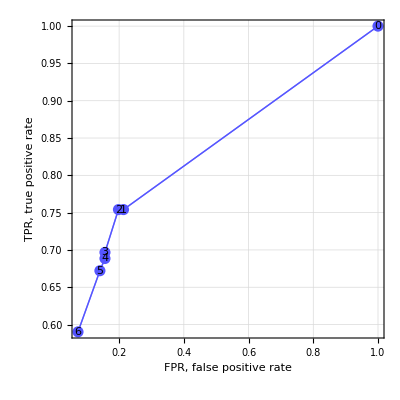

```mathematica
rocRange=Range[0,Length[aCLs]-1,1];
aROCs=Table[(
cres=EnsembleClassifyByThreshold[aCLs,testData⟦All,1;;-2⟧,"survived"->i,"Votes"];ToROCAssociation[{"survived","died"},testData⟦All,-1⟧,cres]),{i,rocRange}];
ROCPlot[rocRange,aROCs,"PlotJoined"->Automatic,GridLines->Automatic]
```

### ROC for ensemble probabilities mean

If we want to compute ROC of a range of probability thresholds we EnsembleClassifyByThreshold with the fourth argument being “ProbabilitiesMean”.

```mathematica
EnsembleClassifyByThreshold[aCLs,testData⟦1;;6,1;;-2⟧,"survived"->0.2,"ProbabilitiesMean"]
```

{survived,survived,survived,survived,survived,survived}

```mathematica
EnsembleClassifyByThreshold[aCLs,testData⟦1;;6,1;;-2⟧,"survived"->0.6,"ProbabilitiesMean"]
```

{survived,died,survived,died,died,survived}

The implementation of EnsembleClassifyByThreshold with “ProbabilitiesMean” relies on the ClassifierFunction signature:

ClassifierFunction[__][record_, "Probabilities"]

Here is the corresponding ROC plot:

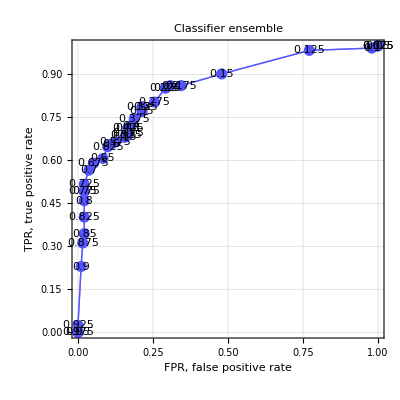

```mathematica
rocRange=Range[0,1,0.025];
aROCs=Table[(
cres=EnsembleClassifyByThreshold[aCLs,testData⟦All,1;;-2⟧,"survived"->i,"ProbabilitiesMean"];ToROCAssociation[{"survived","died"},testData⟦All,-1⟧,cres]),{i,rocRange}];
rocEnGr=ROCPlot[rocRange,aROCs,"PlotJoined"->Automatic,PlotLabel->"Classifier ensemble",GridLines->Automatic]
```

### Comparison of the ensemble classifier with the standard classifiers

This plot compares the ROC curve of the ensemble classifier with the ROC curves of the classifiers that comprise the ensemble.

```mathematica
rocGRs=Table[
aROCs1=Table[(
cres=ClassifyByThreshold[aCLs⟦i⟧,testData⟦All,1;;-2⟧,"survived"->th];
ToROCAssociation[{"survived","died"},testData⟦All,-1⟧,cres]),{th,rocRange}];ROCPlot[rocRange,aROCs1,PlotLabel->Keys[aCLs]⟦i⟧,PlotRange->{{0,1.05},{0.6,1.01}},"PlotJoined"->Automatic,GridLines->Automatic],
{i,1,Length[aCLs]}];
```

Plot the ROC curves for each classifier

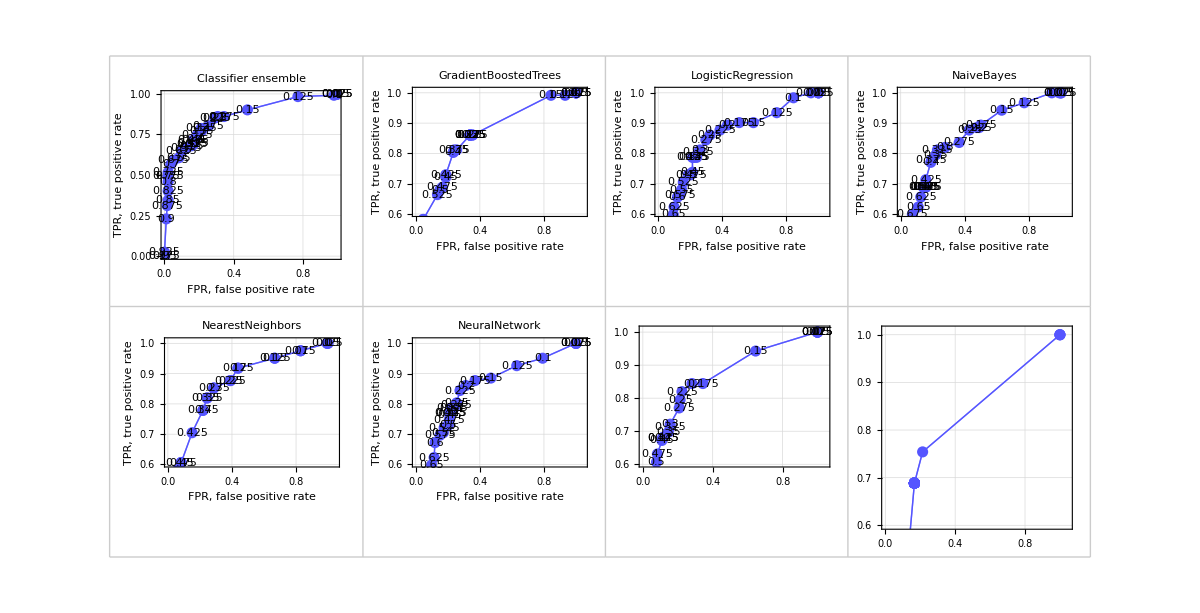

```mathematica
GraphicsGrid[ArrayReshape[Append[Prepend[rocGRs,rocEnGr],rocEnGr],{2,4},""],Dividers->All,FrameStyle->GrayLevel[0.8],ImageSize->1200]
```

Let us plot all ROC curves from the graphics grid above into one plot. For that the single classifier ROC curves are made gray, and their threshold callouts removed. We can see that the classifier ensemble brings very good results for θ=0.175 and none of the single classifiers has a better point.

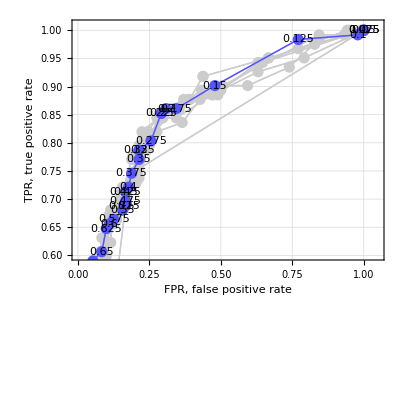

```mathematica
Show[Append[rocGRs/.{RGBColor[___]->GrayLevel[0.8]}/.{Text[p_,___]:>Null}/.((PlotLabel->_):>(PlotLabel->Null)),rocEnGr]]
```

## Classifier ensembles by bootstrapping

There are several ways to produce ensemble classifiers using bootstrapping or jackknife resampling procedures.

First, we are going to make a bootstrapping classifier ensemble using one of the Classify methods. Then we are going to make a more complicated bootstrapping classifier with six methods of Classify.

### Bootstrapping ensemble with a single classification method

First we select a classification method and make a classifier with it.

```mathematica
clMethod="NearestNeighbors";
sCL=Classify[trainingData⟦All,1;;-2⟧->trainingData⟦All,-1⟧,Method->clMethod];
```

The following code makes a classifier ensemble of 12 classifier functions using resampled, slightly smaller (10%) versions of the original training data (with RandomChoice).

```mathematica
SeedRandom[1262];
aBootStrapCLs=Association@Table[(
inds=RandomChoice[Range[Length[trainingData]],Floor[0.9*Length[trainingData]]];
ToString[i]->Classify[trainingData⟦inds,1;;-2⟧->trainingData⟦inds,-1⟧,Method->clMethod]),{i,12}];
```

Let us compare the ROC curves of the single classifier with the bootstrapping derived ensemble.

```mathematica
rocRange=Range[0.1,0.9,0.025];
AbsoluteTiming[
aSingleROCs=Table[(
cres=ClassifyByThreshold[sCL,testData⟦All,1;;-2⟧,"survived"->i];ToROCAssociation[{"survived","died"},testData⟦All,-1⟧,cres]),{i,rocRange}];
aBootStrapROCs=Table[(
cres=EnsembleClassifyByThreshold[aBootStrapCLs,testData⟦All,1;;-2⟧,"survived"->i];ToROCAssociation[{"survived","died"},testData⟦All,-1⟧,cres]),{i,rocRange}];
]
```

{2.47632,Null}

```mathematica
Legended[
Show[{
ROCPlot[rocRange,aSingleROCs,"ROCColor"->Blue,"PlotJoined"->Automatic,GridLines->Automatic],
ROCPlot[rocRange,aBootStrapROCs,"ROCColor"->Red,"PlotJoined"->Automatic]}],
SwatchLegend@@Transpose@{{Blue,Row[{"Single ",clMethod," classifier"}]},{Red,Row[{"Boostrapping ensemble of\n",Length[aBootStrapCLs]," ", clMethod," classifiers"}]}}]
```

-Graphics-

We can see that we get much better results with the bootstrapped ensemble.

### Bootstrapping ensemble with multiple classifier methods

This code creates an classifier ensemble using the classifier methods corresponding to Automatic given as a first argument to EnsembleClassifier.

```mathematica
SeedRandom[2324];
AbsoluteTiming[
aBootStrapLargeCLs=Association@Table[(
inds=RandomChoice[Range[Length[trainingData]],Floor[0.9*Length[trainingData]]];
ecls=EnsembleClassifier[Automatic,trainingData⟦inds,1;;-2⟧->trainingData⟦inds,-1⟧];
AssociationThread[Map[#<>"-"<>ToString[i]&,Keys[ecls]]->Values[ecls]]
),{i,12}];
]
```

RandomGeneratorState[…]

{422.218,Null}

This code computes the ROC statistics with the obtained bootstrapping classifier ensemble:

```mathematica
AbsoluteTiming[
aBootStrapLargeROCs=Table[(
cres=EnsembleClassifyByThreshold[aBootStrapLargeCLs,testData⟦All,1;;-2⟧,"survived"->i];ToROCAssociation[{"survived","died"},testData⟦All,-1⟧,cres]),{i,rocRange}];
]
```

{20.7391,Null}

Let us plot the ROC curve of the bootstrapping classifier ensemble (in blue) and the single classifier ROC curves (in gray):

```mathematica
aBootStrapLargeGr=ROCPlot[rocRange,aBootStrapLargeROCs,"PlotJoined"->Automatic];
Show[Append[rocGRs/.{RGBColor[___]->GrayLevel[0.8]}/.{Text[p_,___]:>Null}/.((PlotLabel->_):>(PlotLabel->Null)),aBootStrapLargeGr],PlotRange->All]
```

-Graphics-

Again we can see that the bootstrapping ensemble produced better ROC points than the single classifiers.

## Damaging data

This section tries to explain why the bootstrapping with resampling to smaller sizes produces good results.

In short, the training data has outliers; if we remove small fraction of the training data we might get better results.

The procedure described in this section can be used in conjunction with the procedures described in the guide for importance of variables investigation [8].

### Ordering function

Let us replace the categorical values with numerical in the training data. There are several ways to do it, here is a fairly straightforward one:

```mathematica
nTrainingData=trainingData/.{"survived"->1,"died"->0,"1st"->0,"2nd"->1,"3rd"->2,"male"->0,"female"->1};
```

### Decreasing proportions of females

First, let us find all indices corresponding to records about females.

```mathematica
femaleInds=Flatten@Position[trainingData⟦All,3⟧,"female"];
```

The following code standardizes the training data corresponding to females, finds the mean record, computes distances from the mean record, and finally orders the female records indices according to their distances from the mean record.

```mathematica
t=Transpose@Map[Rescale@*Standardize,N@Transpose@nTrainingData⟦femaleInds,1;;2⟧];
m=Mean[t];
ds=Map[EuclideanDistance[#,m]&,t];
femaleInds=femaleInds⟦Reverse@Ordering[ds]⟧;
```

The following plot shows the distances calculated above.

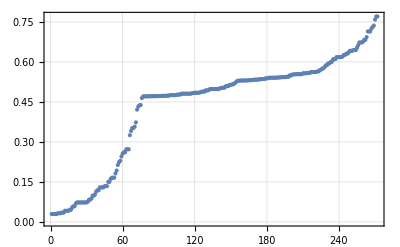

```mathematica
ListPlot[Sort@ds,PlotRange->All,PlotTheme->"Detailed"]
```

The following code removes from the training data the records corresponding to females according to the order computed above. The female records farthest from the mean female record are removed first.

```mathematica
AbsoluteTiming[
femaleFrRes=Association@
Table[cl->
Table[(
inds=Complement[Range[Length[trainingData]],Take[femaleInds,Ceiling[fr*Length[femaleInds]]]];
cf=Classify[trainingData⟦inds,1;;-2⟧->trainingData⟦inds,-1⟧,Method->cl];cfPredictedLabels=cf/@testData⟦All,1;;-2⟧;
{fr,ToROCAssociation[{"survived","died"},testData⟦All,-1⟧,cfPredictedLabels]}),
{fr,0,0.8,0.05}],
{cl,{"NearestNeighbors",{"NeuralNetwork",MaxTrainingRounds->10,"NetworkDepth"->2},"LogisticRegression","RandomForest","SupportVectorMachine","NaiveBayes"}}];
]
```

{130.361,Null}

The following graphics grid shows how the classification results are affected by the removing fractions of the female records from the training data. The results for none or small fractions of records removed are more blue.

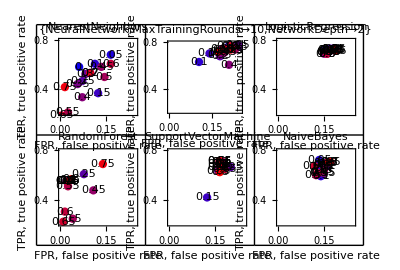

```mathematica
GraphicsGrid[ArrayReshape[
Table[
femaleAROCs=femaleFrRes[cl]⟦All,2⟧;
frRange=femaleFrRes[cl]⟦All,1⟧;ROCPlot[frRange,femaleAROCs,PlotRange->{{0.0,0.25},{0.2,0.8}},PlotLabel->cl,"ROCPointColorFunction"->(Blend[{Blue,Red},#3/Length[frRange]]&),PlotJoined->False,ImageSize->300],
{cl,Keys[femaleFrRes]}],
{2,3}],Dividers->All]
```

We can see that removing the female records outliers has dramatic effect on the results by the classifiers “NearestNeighbors” and “NeuralNetwork”. Not so much on “LogisticRegression” and “NaiveBayes”.

### Decreasing proportions of males

The code in this sub-section repeats the experiment described in the previous one males (instead of females).

```mathematica
maleInds=Flatten@Position[trainingData⟦All,3⟧,"male"];
```

```mathematica
t=Transpose@Map[Rescale@*Standardize,N@Transpose@nTrainingData⟦maleInds,1;;2⟧];
m=Mean[t];
ds=Map[EuclideanDistance[#,m]&,t];
maleInds=maleInds⟦Reverse@Ordering[ds]⟧;
```

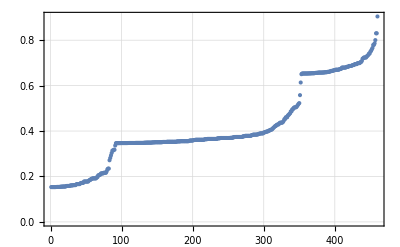

```mathematica
ListPlot[Sort@ds,PlotRange->All,PlotTheme->"Detailed"]
```

```mathematica
AbsoluteTiming[
maleFrRes=Association@
Table[cl->
Table[(
inds=Complement[Range[Length[trainingData]],Take[maleInds,Ceiling[fr*Length[maleInds]]]];
cf=Classify[trainingData⟦inds,1;;-2⟧->trainingData⟦inds,-1⟧,Method->cl];cfPredictedLabels=cf/@testData⟦All,1;;-2⟧;
{fr,ToROCAssociation[{"survived","died"},testData⟦All,-1⟧,cfPredictedLabels]}),
{fr,0,0.8,0.05}],
{cl,{"NearestNeighbors",{"NeuralNetwork",MaxTrainingRounds->10,"NetworkDepth"->2},"LogisticRegression","RandomForest","SupportVectorMachine","NaiveBayes"}}];
]
```

{133.737,Null}

Plot  ROC points (not curves)

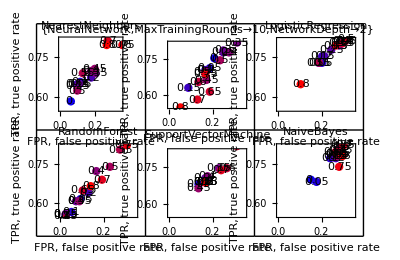

```mathematica
GraphicsGrid[ArrayReshape[
Table[
maleAROCs=maleFrRes[cl]⟦All,2⟧;
frRange=maleFrRes[cl]⟦All,1⟧;ROCPlot[frRange,maleAROCs,PlotRange->{{0.0,0.35},{0.55,0.82}},PlotLabel->cl,"ROCPointColorFunction"->(Blend[{Blue,Red},#3/Length[frRange]]&),PlotJoined->False,ImageSize->300],
{cl,Keys[maleFrRes]}],
{2,3}],Dividers->All]
```

## Classifier interpolation

Assume that we want a classifier that for a given representative set of n items (records) assigns the positive label to an exactly n_p of them. (Or very close to that number.)

If we have two classifiers, one returning more positive items than n_p, the other less than n_p, then we can use geometric computations in the ROC space in order to obtain parameters for a classifier interpolation that will bring positive items close to n_p; see [3]. Below is given Mathematica code with explanations of how that classifier interpolation is done.

Assume that by prior observations we know that for a given dataset of n items the positive class consists of ≈0.09n items. Assume that for a given unknown dataset of n items we want n_p=0.2 n of the items to be classified as positive. We can write the equation:

FPR ((1 - 0.09) n) + TPR (0.09 n) == 0.2 n

which can be simplified to

FPR (1 - 0.09) + TPR 0.09 == 0.2

### The two classifiers

Consider the following two classifiers.

```mathematica
cf1=Classify[trainingData⟦All,1;;-2⟧->trainingData⟦All,-1⟧,Method->"RandomForest"];
cfROC1=ToROCAssociation[{"survived","died"},testData⟦All,-1⟧,cf1[testData⟦All,1;;-2⟧]]
```

<|TruePositive→81,FalsePositive→21,TrueNegative→171,FalseNegative→41|>

```mathematica
cf2=Classify[trainingData⟦All,1;;-2⟧->trainingData⟦All,-1⟧,Method->"LogisticRegression"];
cfROC2=ToROCAssociation[{"survived","died"},testData⟦All,-1⟧,cf2[testData⟦All,1;;-2⟧]]
```

<|TruePositive→89,FalsePositive→36,TrueNegative→156,FalseNegative→33|>

### Geometric computations in the ROC space

Here are the ROC space points corresponding to the two classifiers, cf1 and cf2:

```mathematica
p1=Through[ROCFunctions[{"FPR","TPR"}][cfROC1]];
p2=Through[ROCFunctions[{"FPR","TPR"}][cfROC2]];
```

Here is the breakdown of frequencies of the class labels:

```mathematica
Tally[trainingData⟦All,-1⟧]
%⟦All,2⟧/Length[trainingData]//N
```

{{survived,305},{died,427}}

{0.416667,0.583333}

We want to our classifier to produce 38% people to survive. Here we find two points of the corresponding constraint line (on which we ROC points of the desired classifiers should reside):

```mathematica
sol1=Solve[{{x,y}∈ImplicitRegion[{x(1-0.42)+y 0.42==0.38},{x,y}],x==0.1},{x,y}]⟦1⟧
sol2=Solve[{{x,y}∈ImplicitRegion[{x(1-0.42)+y 0.42==0.38},{x,y}],x==0.25},{x,y}]⟦1⟧
```

{x→0.1,y→0.766667}

{x→0.25,y→0.559524}

Here using the points q1 and q2 of the constraint line we find the intersection point with the line connecting the ROC points of the classifiers:

```mathematica
{q1,q2}={{x,y}/.sol1,{x,y}/.sol2};
sol=Solve[ {{x,y}∈InfiniteLine[{q1,q2}]∧{x,y}∈InfiniteLine[{p1,p2}]},{x,y}];
q={x,y}/.sol⟦1⟧
```

{0.149814,0.697876}

Let us plot all geometric objects:

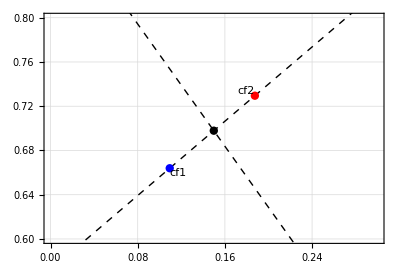

```mathematica
Graphics[{PointSize[0.015],Blue,Tooltip[Point[p1],"cf1"],Black,Text["cf1",p1,{-1.5,1}],Red,Tooltip[Point[p2],"cf2"],Black,Text["cf2",p2,{1.5,-1}],Black,Point[q],Dashed,InfiniteLine[{q1,q2}],Thin,InfiniteLine[{p1,p2}]},PlotRange->{{0.,0.3},{0.6,0.8}},GridLines->Automatic,Frame->True]
```

### Classifier interpolation

Next we find the ratio of the distance from the intersection point q to the cf1 ROC point and the distance between the ROC points of cf1 and cf2.

```mathematica
k=Norm[p1-q]/Norm[p1-p2]
```

0.517615

The classifier interpolation is made by a weighted random selection based on that ratio (using RandomChoice):

RandomGeneratorState[…]

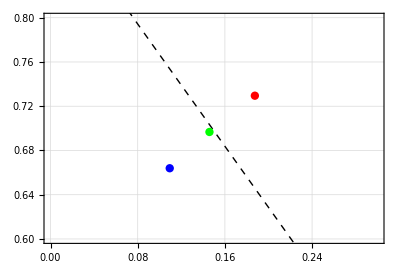

```mathematica
SeedRandom[8989]
cres=MapThread[If,{RandomChoice[{1-k,k}->{True,False},Length[testData]],cf1@testData⟦All,1;;-2⟧,cf2@testData⟦All,1;;-2⟧}];
cfROC3=ToROCAssociation[{"survived","died"},testData⟦All,-1⟧,cres];
p3=Through[ROCFunctions[{"FPR","TPR"}][cfROC3]];
Graphics[{PointSize[0.015],Blue,Point[p1],Red,Point[p2],Black,Dashed,InfiniteLine[{q1,q2}],Green,Point[p3]},PlotRange->{{0.,0.3},{0.6,0.8}},GridLines->Automatic,Frame->True]
```

We can run the process multiple times in order to convince ourselves that the interpolated classifier ROC point is very close to the constraint line most of the time.

```mathematica
p3s=
Table[(
cres=MapThread[If,{RandomChoice[{1-k,k}->{True,False},Length[testData]],cf1@testData⟦All,1;;-2⟧,cf2@testData⟦All,1;;-2⟧}];cfROC3=ToROCAssociation[{"survived","died"},testData⟦All,-1⟧,cres];
Through[ROCFunctions[{"FPR","TPR"}][cfROC3]]),{1000}];
```

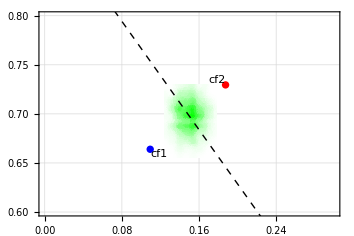

```mathematica
Show[
{SmoothDensityHistogram[p3s,ColorFunction->(Blend[{White,Green},#]&),Mesh->3],Graphics[{PointSize[0.015],Blue,Tooltip[Point[p1],"cf1"],Black,Text["cf1",p1,{-1.5,1}],Red,Tooltip[Point[p2],"cf2"],Black,Text["cf2",p2,{1.5,-1}],Black,Dashed,InfiniteLine[{q1,q2}]},GridLines->Automatic]},PlotRange->{{0.,0.3},{0.6,0.8}},GridLines->Automatic,Axes->True,AspectRatio->Automatic]
```

## References

[1] Leo Breiman, Statistical Modeling: The Two Cultures, (2001), Statistical Science, Vol. 16, No. 3, 199–231.

[2] Wikipedia entry, Receiver operating characteristic. URL: http://en.wikipedia.org/wiki/Receiver_operating_characteristic .

[3] Tom Fawcett, An introduction to ROC analysis, (2006), Pattern Recognition Letters, 27, 861–874. (Link to PDF.)

[4] Anton Antonov, DataReshapers WL paclet, (2023), Wolfram Language Paclet Repository.

[5] Anton Antonov, ROCFunctions WL paclet, (2023), Wolfram Language Paclet Repository.

[6] Anton Antonov, ClassifierEnsembles WL paclet, (2024), Wolfram Language Paclet Repository.

[7] Anton Antonov, “Importance of variables investigation guide”, (2016),  MathematicaForPrediction at GitHub.

Related Guides

Ensembles of classifiers

Related Tech Notes

## Metadata

### Categorization

Tech Note

AntonAntonov/ClassifierEnsembles

AntonAntonov`ClassifierEnsembles`

AntonAntonov/ClassifierEnsembles/tutorial/ROCforclassifierensemblesbootstrappingdamagingandinterpolation

### Keywords

Classifier ensembles

Receiver Operating Characteristic

ROC

Bootstrapping